# FiberDiameter effect on temperature rise (141118)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
samplingRate=1000./128
```

7.8125

```mathematica
gagFiles=FileNames["*.mat"]
```

{140917-01-200um-2,5mW,500ms,0'2Hz,40T(Blood vessel).mat,140917-02-200um-2,5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-03-200um-5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-04-100um-5mW,500ms,0'2Hz,40T(No Blood vessel).mat,140917-05-400um-5mW,500ms,0'2Hz,40T(Half Blood vessel).mat,140917-06-200um-2,5mW,10000ms,0'05Hz,20T.mat}

## 5 mW 500 ms

## Functions

```mathematica
baselineNormalize[data_]:=Module[{},
(#-Mean[#[[1;;9]]])&/@data
];
```

```mathematica
meanBandPlot[data_, color_]:=Module[{means, sds},
means=Mean/@Transpose[data];
sds=StandardDeviation/@Transpose[data];
ListLinePlot[{means-sds, means+sds},
PlotStyle->None,
PlotRange->All,
Filling->{1->{{2},Opacity[1,color]}}
]
];
```

```mathematica
meanPlot[data_, color_, dataRange_:Automatic]:=
Module[{means,timePoints},
means=Mean/@Transpose[data];
If[dataRange===Automatic,
ListLinePlot[means,PlotStyle->{color,Thick}],
timePoints=Rescale[Range[Length[means]],{1,Length[means]},dataRange];
ListLinePlot[Transpose[{timePoints,means}],
PlotStyle->{color,Thick},PlotRange->All]
]


];
```

```mathematica
means[data_]:=Module[{means, sds},
Mean/@Transpose[data]
];
```

```mathematica
trialPointPlot[data_, color_]:=Module[{},
ListPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
trialPointLogPlot[data_, color_]:=Module[{},
ListLogPlot[data,PlotStyle->Opacity[0.2,color]]
];
```

```mathematica
gagColors= {LightBlue,Blue,Darker[Blue],Purple,Pink,Red,Orange,Yellow,LightGreen,Green, Darker[Green]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gagColors=Table[ColorData["GrayTones",1-n],{n,0.2,1,0.8/2}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Load Data

```mathematica
gagFitDataFiberDiam=Map[Import,gagFiles];
Dimensions/@gagFitDataFiberDiam
```

{{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,40,620},{1,20,2540}}

```mathematica
gagFitDataFiberDiam= gagFitDataFiberDiam[[{4,3,5}]];
Dimensions[gagFitDataFiberDiam]
```

{3,1,40,620}

```mathematica
gagFitDataFiberDiam=Flatten[gagFitDataFiberDiam,1];
Dimensions/@gagFitDataFiberDiam
```

{{40,620},{40,620},{40,620}}

### Remove bad trials if necessary

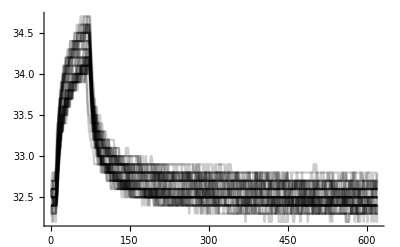
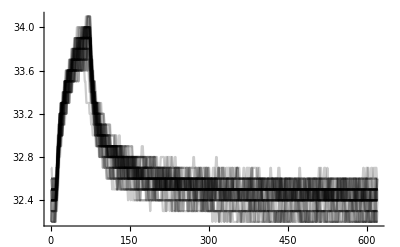
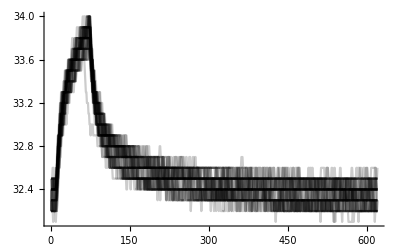

```mathematica
ListLinePlot[#,PlotStyle->Opacity[0.2,Black],PlotRange->All]&/@gagFitDataFiberDiam
```

```mathematica
gagTemp=ListLinePlot[gagFitDataFiberDiam[[3]],PlotStyle->Opacity[0.2,Black],PlotRange->All]
```

-Graphics-

```mathematica
Ordering[gagFitDataFiberDiam[[2]][[;;, 1]],1]
```

{31}

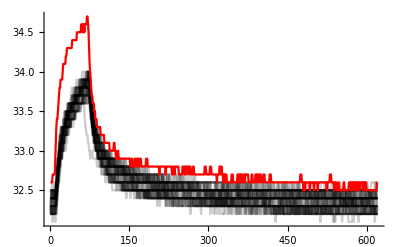

```mathematica
Show[gagTemp, ListLinePlot[gagFitDataFiberDiam[[1]][[11]],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
gagFitDataFiberDiam[[3]]=Delete [gagFitDataFiberDiam[[3]],{{39},{40}}];
Dimensions[gagFitDataFiberDiam[[3]]]
```

{38,620}

## Normalize Data so Baseline is at 0, Set Range Variables

```mathematica
Dimensions/@gagFitDataFiberDiam
```

{{40,620},{40,620},{38,620}}

```mathematica
gagFitDataFiberDiam=baselineNormalize/@ gagFitDataFiberDiam;
```

```mathematica
Dimensions/@gagFitDataFiberDiam
```

{{40,620},{40,620},{38,620}}

```mathematica
501/(1000/128.) (*figuring out stim duration*)
```

64.128

```mathematica
stimDuration=64;
stimStart=11;
stimEnd=stimStart+stimDuration-4;
fallStart=stimStart+stimDuration-1;
fallEnd=fallStart+200;
trialLength=Length[gagFitDataFiberDiam[[1, 1]]]
```

620

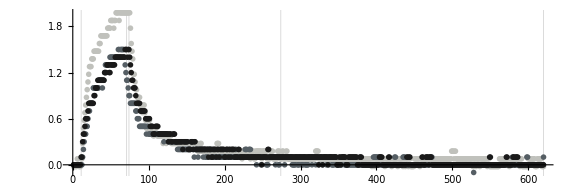

```mathematica
gagTempFitDataFiberDiam=ListPlot[gagFitDataFiberDiam[[All,1]],PlotRange->All,
GridLines->{{stimStart,stimEnd,fallStart,fallEnd,trialLength},None}, 
AspectRatio->1/3, ImageSize->72*8,PlotStyle->gagColors]
```

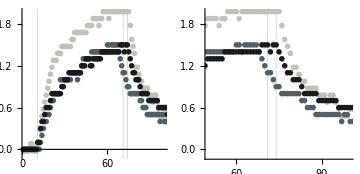

```mathematica
GraphicsRow[
{Show[gagTempFitDataFiberDiam,PlotRange->{{0,100},All},AspectRatio->1],
Show[gagTempFitDataFiberDiam,PlotRange->{stimStart+stimDuration+{-25,+25},All},AspectRatio->1]}, ImageSize->Medium]
```

## Cleaner Plots

```mathematica
Dimensions[Transpose[{gagFitDataFiberDiam,gagColors}]]
```

{3,2}

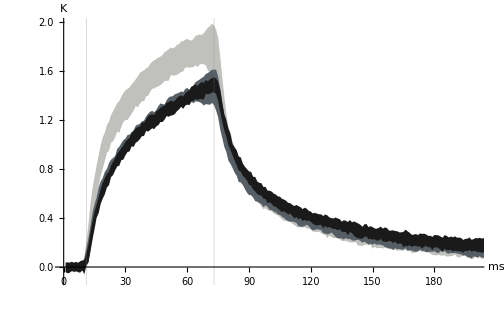

```mathematica
grSDFiberDiam=Show[meanBandPlot[#[[1]],#[[2]]]& /@ Transpose[{gagFitDataFiberDiam,gagColors}],
GridLines->{{stimStart,stimEnd+2},None}, PlotRange->{{0,200},All},AspectRatio->1/GoldenRatio,ImageSize->72*7, AxesLabel->{"ms", "K"},Ticks->{Automatic,Automatic}, 
AxesStyle->Thickness[0.0025], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0,0}]
```

```mathematica
legend={"100","200","400"};
```

```mathematica
gagLegend=Graphics[
Table[
{gagColors[[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,2}], PlotLabel->Style["Fiber Diameter [μm]",FontWeight->Bold,FontColor->Black,FontSize->9], AspectRatio->1/10,ImageSize->72*1.5
]
```

-Graphics-

```mathematica
(*gagLegend=LineLegend[gagColors,legend,LegendLayout->"Column",LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"FiberDiamer [um]"]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{0,200}},LegendMarkers-> {{20,40}},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend=Graphics[
Table[
{gagColors[[n+1]],EdgeForm[Directive[Thin,Black]],Rectangle[{-10+n*20, 0},{10+n*20, 5}], Black, Text[legend[[n+1]],{n*20, 0},{0,1.5},BaseStyle->{FontSize->9,Bold}]}, 
{n,0,3}], PlotLabel->Style["FiberDiamer [mW]",FontWeight->Bold], AspectRatio->0.9/10,ImageSize->72*3
]
```

```mathematica
(*gagLegend=BarLegend[{gagColors,{-10,210}},10,LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->5,LegendLayout->"Row",LegendLabel->"Lapsed Time [mins]"]*)
```

```mathematica
(*gagLegend2= SwatchLegend[{Opacity[0.15,Blue]}, {"Laser Stimulation"},LabelStyle->{FontSize->10,FontWeight->"Bold"},LegendMargins->{{53,54},{5,5}},LegendLayout->"Row",LegendFunction->(Framed[#]&)]*)
```

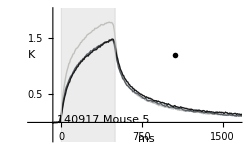

```mathematica
grSDFiberDiam=Show[
Show[meanPlot[#[[1]],#[[2]],{-11,620-11}*samplingRate]& /@ Transpose[{gagFitDataFiberDiam,gagColors}],ImageSize->72*3.5,
GridLines->{{0,500},None},GridLinesStyle->Thickness[0.0025],PlotRange->{{-35,210}*samplingRate,{-0.3,2}},AspectRatio->1/GoldenRatio, AxesLabel->{None, None},Ticks->{Table[n,{n,0,1500,250}],{0.5,1,1.5,2}},TicksStyle->Directive[Black,9],
AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{-10*samplingRate,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
(*PlotLabel->  "Average temperature increase through time",*)
Prolog->{Opacity[0.15,Gray], Rectangle[{0,-1},{500,7}]},
Epilog->{Text["ms",{101*samplingRate,-0.3},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Text["K",{-35*samplingRate,1.2},BaseStyle->{FontSize->9,FontWeight->"Bold"}],
Inset[gagLegend,{135*samplingRate,1.2}],Text["140917 Mouse 5",{50*samplingRate,0.05},BaseStyle->{FontSize->2}]}]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.AverageFiberDiam.png",grSDFiberDiam,ImageResolution->600]
```

140917.AverageFiberDiam.png

```mathematica
Export["140917.AverageFiberDiam.pdf",grSDFiberDiam,ImageResolution->600]
```

140917.AverageFiberDiam.pdf

```mathematica
gagMeanDataFiberDiam= Mean/@gagFitDataFiberDiam;
```

```mathematica
Dimensions[gagMeanDataFiberDiam]
```

{3,620}

```mathematica
gagMaxDataFiberDiam=Max/@gagMeanDataFiberDiam
```

{1.79,1.47611,1.48713}

```mathematica
gagMaxDataFiberDiam=Map[ToString[NumberForm[#,{3,2}],OutputForm]&,gagMaxDataFiberDiam,{1}]
```

{1.79,1.48,1.49}

```mathematica
gagMaxDataFiberDiam=ToExpression[gagMaxDataFiberDiam]
```

{1.79,1.48,1.49}

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

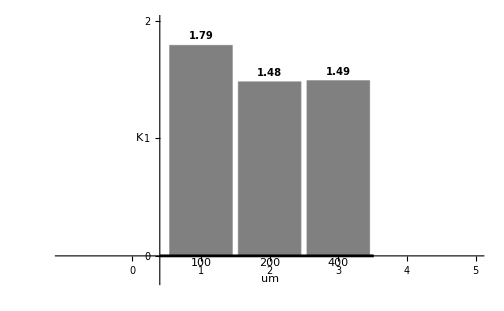

```mathematica
gagMaxTempGraph=BarChart[gagMaxDataFiberDiam,
PlotRange->{{-1,5},{-0.2,2}},
ChartLabels->{{"100","200","400"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{{0,1,2,3,4,5,6}},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["um",{2,-0.2},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Text["K",{0.1,1},BaseStyle->{FontSize->12,FontWeight->"Bold"}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.FiberDiamMaxTemp.png",gagMaxTempGraph]
```

140917.FiberDiamMaxTemp.png

```mathematica
Export["140917.FiberDiamMaxTemp.pdf",gagMaxTempGraph]
```

140917.FiberDiamMaxTemp.pdf

## Change data to {{time,value}, ....} format and Fit Functions

```mathematica
gagMakeTrialXY[data_, startPoint_Integer, endPoint_Integer]:=Module[{gagTimecourseR},
gagTimecourseR =Range[0, endPoint-startPoint ] *samplingRate;
Flatten[ 
Transpose[{gagTimecourseR,#[[startPoint;;endPoint]]}]&  /@ data,   1
]
];
```

```mathematica
gagModelModelRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc, tempShift},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{0.4*a*Log[0.01*c* x+0.1*b]},
{a,b,c},x]]] 
];
```

```mathematica
gagModelShiftFactorRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc,tempShift},
tempFunc=gagModelFuncRLog[data, startPoint, endPoint];
tempShift= x /. Flatten[Solve[ Evaluate[tempFunc[x]]==0, x]];
tempShift
];
```

```mathematica
gagModelFuncRLog[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelRLog[data, startPoint, endPoint]["BestFit"];
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
gagModelModelFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{},
Simplify[Evaluate[
NonlinearModelFit[gagMakeTrialXY[data,startPoint, endPoint],  
{a*ⅇ^(b*(x+7)) +aa*ⅇ^(b*bb*(x+90)),{0 < a<5,-0.5<b<-0.0001 ,0<aa<5,0<bb<1}},
{a,c,b,aa,bb,cc},x]]]
];
```

```mathematica
gagModelFuncFExp[data_, startPoint_Integer, endPoint_Integer]:=
Module[{tempFunc},
tempFunc=gagModelModelFExp[data, startPoint, endPoint]["BestFit"] ;
Evaluate[tempFunc /. x->#]&
];
```

```mathematica
Manipulate[
Show[grSDFiberDiam,Plot[a*ⅇ^(b*(x)) +aa*ⅇ^(bb*(x)),{x,fallStart,trialLength},PlotRange->All],
PlotRange->All],
{{a,230.},0,1500},{{b,-0.0612},-0.2,0.2},{{aa,0.31},0,5},{{bb,0.0075},-1,0.3}
];
```

## Fit Function BootStrap

```mathematica
gagBootStrapData=Table[RandomSample[#,10],{500}]& /@gagFitDataFiberDiam;
Dimensions[gagBootStrapData]
```

{3,500,10,620}

```mathematica
gagBootStrapModel= ParallelMap[gagModelModelRLog[#,stimStart, stimEnd]&, gagBootStrapData[[#]]]& /@Range[3];
Dimensions[gagBootStrapModel]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{3,500}

```mathematica
gagBootStrapModelParams=#["BestFitParameters"]&/@gagBootStrapModel[[#]]&/@Table[x,{x,1,3,1}];
Dimensions[gagBootStrapModelParams]
```

{3,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,3,500}

```mathematica
gagBootStrapModelParams={a/.#& /@gagBootStrapModelParams[[;;,1,#]]*0.4&/@Table[x,{x,1,500,1}],b/.#& /@gagBootStrapModelParams[[;;,2,#]]*0.1&/@Table[x,{x,1,500,1}],c/.#& /@gagBootStrapModelParams[[;;,3,#]]*0.01&/@Table[x,{x,1,500,1}]};
Dimensions[gagBootStrapModelParams]
```

{3,500,3}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{1,3,2}];
Dimensions[gagBootStrapModelParams]
```

{3,3,500}

```mathematica
gagBootStrapModelParams=Transpose[gagBootStrapModelParams,{2,1,3}];
Dimensions[gagBootStrapModelParams]
```

{3,3,500}

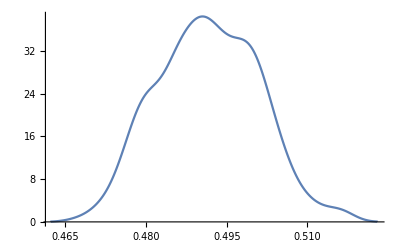
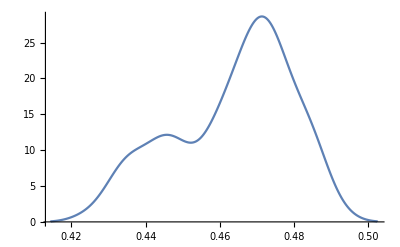
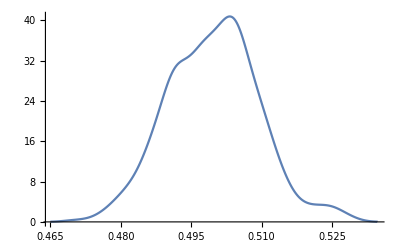
5
6[{{-Graphics-,0.133183},{-Graphics-,0},{-Graphics-,0.244117}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,1]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,3,1}]//TableForm[{5,6}]
```

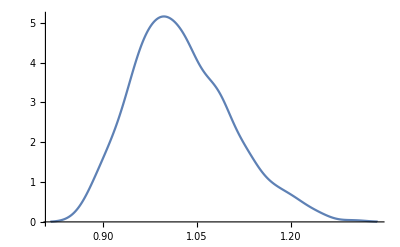
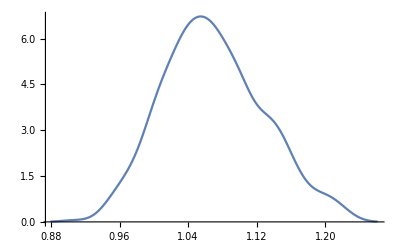
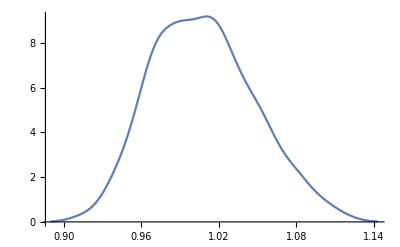
5
6[{{-Graphics-,0.133183},{-Graphics-,0},{-Graphics-,0.244117}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,2]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,3,1}]//TableForm[{5,6}]
```

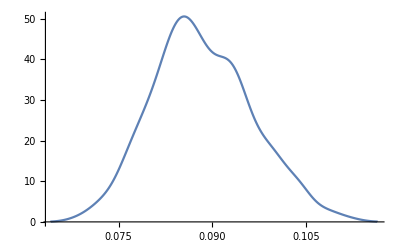
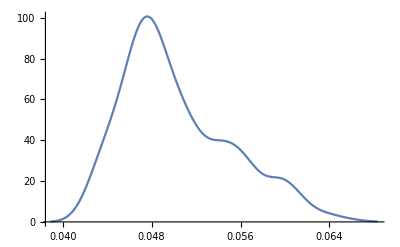
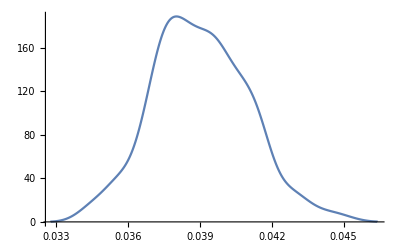
5
6[{{-Graphics-,0.133183},{-Graphics-,0},{-Graphics-,0.244117}}]

```mathematica
{SmoothHistogram[gagBootStrapModelParams[[#,3]]],DistributionFitTest[gagBootStrapModelParams[[#,1]]]}&/@Table[x,{x,1,3,1}]//TableForm[{5,6}]
```

```mathematica
gagBootStrapModelParamsMedian=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[3]];
Dimensions[gagBootStrapModelParamsMedian]
```

{3,3}

```mathematica
gagBootStrapModelParams99= Transpose[Quantile[#,{0.01,0.99},{{1/2,0},{0,1}}]&/@gagBootStrapModelParams[[#]]&/@Range[3],{2,1,3}];
Dimensions[gagBootStrapModelParams99]
```

{3,3,2}

```mathematica
gagBootStrapModelParamsMedian0=gagBootStrapModelParamsMedian;
```

```mathematica
gagBootStrapModelParamsMedian0={Range[3],#}&/@gagBootStrapModelParamsMedian0;
Dimensions[gagBootStrapModelParamsMedian0]
```

{3,2,3}

```mathematica
gagBootStrapModelParamsMedian0=Transpose[gagBootStrapModelParamsMedian0,{1,3,2}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

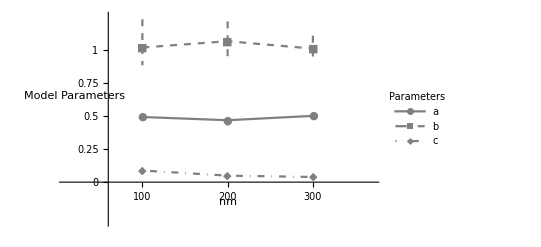

```mathematica
gagAvalueBootStrapGraph=ErrorListPlot[
Transpose[{gagBootStrapModelParamsMedian0,
Map[ErrorBar,
(gagBootStrapModelParams99-gagBootStrapModelParamsMedian0[[;;,;;,2]]),
{2}
]
},{3,1,2}],

Joined->True,
PlotRange->{{0.1,3.7},{-0.3,1.25}},AspectRatio->1/GoldenRatio,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{0.97,0.55},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"100"},{2,"200"},{3,"300"}},{0,0.25,0.5,0.75,1}},Epilog->{Text["nm",{2,-0.15},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.2,0.65},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.C-valueFiberDiamBootstrap.png",gagAvalueBootStrapGraph]
```

140917.C-valueFiberDiamBootstrap.png

```mathematica
Export["140917.C-valueFiberDiamBootstrap.pdf",gagAvalueBootStrapGraph]
```

140917.C-valueFiberDiamBootstrap.pdf

```mathematica
gagBootStrapModelParamsMedian0
```

{{{1,0.491428},{2,0.467059},{3,0.500002}},{{1,1.01572},{2,1.06322},{3,1.00732}},{{1,0.0876522},{2,0.0490344},{3,0.0389112}}}

```mathematica
gagBootStrapModelParamsMedian1=Transpose[Median[#]&/@gagBootStrapModelParams[[#]]&/@Range[3]]
```

{{0.491428,0.467059,0.500002},{1.01572,1.06322,1.00732},{0.0876522,0.0490344,0.0389112}}

```mathematica
gagBootStrapModelParamsMedian1=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParamsMedian1
```

{{0.49, 0.47, 0.50},{1.02, 1.06, 1.01},{0.09, 0.05, 0.04}}

```mathematica
gagBootStrapModelParamsMedian1=ToExpression[gagBootStrapModelParamsMedian1]
```

{{0.49,0.47,0.5},{1.02,1.06,1.01},{0.09,0.05,0.04}}

```mathematica
gagBootStrapModelParams991=ToString[NumberForm[#,{3,2}]]&/@gagBootStrapModelParams99
```

{{{0.47, 0.52}, {0.43, 0.49}, {0.48, 0.52}},{{0.88, 1.23}, {0.95, 1.21}, {0.93, 1.10}},{{0.07, 0.11}, {0.04, 0.06}, {0.03, 0.04}}}

```mathematica
gagBootStrapModelParams991=ToExpression[gagBootStrapModelParams991]
```

{{{0.47,0.52},{0.43,0.49},{0.48,0.52}},{{0.88,1.23},{0.95,1.21},{0.93,1.1}},{{0.07,0.11},{0.04,0.06},{0.03,0.04}}}

```mathematica
gagBootStrapModelParams991=gagBootStrapModelParams991-gagBootStrapModelParamsMedian1
```

{{{-0.02,0.03},{-0.04,0.02},{-0.02,0.02}},{{-0.14,0.21},{-0.11,0.15},{-0.08,0.09}},{{-0.02,0.02},{-0.01,0.01},{-0.01,0.}}}

```mathematica
gagCValueBootStrapData=Table[gagBootStrapModelParamsMedian1[[i,j]]->gagBootStrapModelParams991[[i,j]],{i,1,Length[gagBootStrapModelParamsMedian1]},{j,1,Length[gagBootStrapModelParamsMedian1[[1]]]}]
```

{{0.49→{-0.02,0.03},0.47→{-0.04,0.02},0.5→{-0.02,0.02}},{1.02→{-0.14,0.21},1.06→{-0.11,0.15},1.01→{-0.08,0.09}},{0.09→{-0.02,0.02},0.05→{-0.01,0.01},0.04→{-0.01,0.}}}

```mathematica
errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{errorN,errorP},{errorN=Flatten[meta],errorP=Flatten[meta]};
{errorN,errorP}=If[{errorN,errorP}==={},0,Last[{errorN,errorP}]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Thickness[0.0035],Line[{{{(x0+x1)/2,y1+errorN},{(x0+x1)/2,y1+errorP}},{{1/4 (3 x0+x1),y1+errorP},{1/4 (x0+3 x1),y1+errorP}},{{1/4 (3 x0+x1),y1+errorN},{1/4 (x0+3 x1),y1+errorN}}}]}}]
```

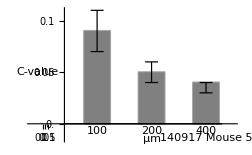

```mathematica
gagCValueBootStrapGraph=BarChart[gagCValueBootStrapData[[3]],ChartElementFunction->errorBar["Rectangle"],ImageSize->72*3.5,
PlotRange->{{-0.2,3.5},{-0.015,0.11}},
ChartLabels->{{"100","200","400"}},LabelStyle->{FontSize->9,FontWeight->"Bold"},BarSpacing->1.1,ChartBaseStyle->EdgeForm[Thickness[0.00595]],
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->9],Directive[Black,Thickness[0.004],FontSize->9]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->9,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.1,0.025}]},TicksStyle->Directive[Black,9],ChartStyle->Gray,TicksStyle->Bold,
LabelStyle->{FontWeight->Bold,FontSize->9},
Epilog->{Text["μm",{2,-0.015},BaseStyle->{FontSize->9,FontWeight->"Bold"}],Rotate[Text["C-value",{-0.1,0.05},BaseStyle->{FontSize->9,FontWeight->"Bold"}],90 Degree],Text["140917 Mouse 5",{3,-0.014},BaseStyle->{FontSize->2}]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.FiberDiamC-ValueBootStrap.png",gagCValueBootStrapGraph,ImageResolution->600]
```

140917.FiberDiamC-ValueBootStrap.png

```mathematica
Export["140917.FiberDiamC-ValueBootStrap.pdf",gagCValueBootStrapGraph,ImageResolution->600]
```

140917.FiberDiamC-ValueBootStrap.pdf

```mathematica
gagBootStrapModelParamsMedian={gagBootStrapModelParamsMedian,gagBootStrapModelParams99};
```

```mathematica
Dimensions[gagBootStrapModelParamsMedian]
```

{2,3,3}

```mathematica
gagBootStrapModelParamsMedian=Transpose[gagBootStrapModelParamsMedian,{3,1,2}]
Dimensions[gagBootStrapModelParamsMedian]
```

{{{0.491428,{0.471787,0.515575}},{0.467059,{0.427684,0.49015}},{0.500002,{0.478249,0.524938}}},{{1.01572,{0.881538,1.22907}},{1.06322,{0.950308,1.2124}},{1.00732,{0.930523,1.10479}}},{{0.0876522,{0.0718914,0.108314}},{0.0490344,{0.04252,0.0633852}},{0.0389112,{0.0345954,0.0442424}}}}

{3,3,2}

```mathematica
gagBootStrapModelParamsMedian=Map[(ToString[NumberForm[#[[1]],{3,2}]] <> " ("<>ToString[NumberForm[#[[2,1]],{3,2}]]<>"-"<>ToString[NumberForm[#[[2,2]],{3,2}]]<>")" )&, gagBootStrapModelParamsMedian,{2}]
```

{{0.49 (0.47-0.52),0.47 (0.43-0.49),0.50 (0.48-0.52)},{1.02 (0.88-1.23),1.06 (0.95-1.21),1.01 (0.93-1.10)},{0.09 (0.07-0.11),0.05 (0.04-0.06),0.04 (0.03-0.04)}}

```mathematica
gagBootStrapModelParamsMedian=Prepend[gagBootStrapModelParamsMedian,{"FiberDiamer [μm]",100,200,400}];
Dimensions[gagBootStrapModelParamsMedian]
```

{4}

```mathematica
gagBootStrapModelParamsMedian[[2]]
```

{0.49 (0.47-0.52),0.47 (0.43-0.49),0.50 (0.48-0.52)}

```mathematica
gagBootStrapModelParamsMedian[[2]]= Prepend[gagBootStrapModelParamsMedian[[2]],"a (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[3]]= Prepend[gagBootStrapModelParamsMedian[[3]],"b (1%CI-99%CI)"];
```

```mathematica
gagBootStrapModelParamsMedian[[4]]= Prepend[gagBootStrapModelParamsMedian[[4]],"c (1%CI-99%CI)"];
```

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
gagBootStrapModelParamsMedian//InputForm
```

{{"FiberDiamer [μm]", 100, 200, 400}, {"a (1%CI-99%CI)", "0.49 (0.47-0.52)", "0.47 (0.43-0.49)", "0.50 (0.48-0.52)"}, {"b (1%CI-99%CI)", "1.02 (0.88-1.23)", "1.06 (0.95-1.21)", "1.01 (0.93-1.10)"}, 
 {"c (1%CI-99%CI)", "0.09 (0.07-0.11)", "0.05 (0.04-0.06)", "0.04 (0.03-0.04)"}}

```mathematica
gagParamsTableBootStrap=Grid[gagBootStrapModelParamsMedian,Frame->All,ItemSize->{{1->9,2;;12->8},1.5},BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}},Background->{None,{4->Opacity[0.35,Gray]}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

FiberDiamer [μm] | 100 | 200 | 400
a (1%CI-99%CI) | 0.49 (0.47-0.52) | 0.47 (0.43-0.49) | 0.50 (0.48-0.52)
b (1%CI-99%CI) | 1.02 (0.88-1.23) | 1.06 (0.95-1.21) | 1.01 (0.93-1.10)
c (1%CI-99%CI) | 0.09 (0.07-0.11) | 0.05 (0.04-0.06) | 0.04 (0.03-0.04)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.ParamsTableFibDiamBootStrap.png",gagParamsTableBootStrap,ImageResolution->600]
```

140917.ParamsTableFibDiamBootStrap.png

```mathematica
Export["140917.ParamsTableFibDiamBootStrap.pdf",gagParamsTableBootStrap,ImageResolution->600]
```

140917.ParamsTableFibDiamBootStrap.pdf

## Fit Function

```mathematica
{funcR1,funcR2, funcR3}=gagModelFuncRLog[#,stimStart, stimEnd]& /@gagFitDataFiberDiam
```

{0.49124 Log[1.02253+0.0878867 #1]&,0.463089 Log[1.06781+0.0500459 #1]&,0.499458 Log[1.00892+0.0389959 #1]&}

```mathematica
{modelR1,modelR2, modelR3}=gagModelModelRLog[#,stimStart, stimEnd]& /@gagFitDataFiberDiam;
```

```mathematica
gagModelParams={modelR1["BestFitParameters"],modelR2["BestFitParameters"],modelR3["BestFitParameters"]};
```

```mathematica
gagModelParams=Transpose[gagModelParams]
```

{{a→1.2281,a→1.15772,a→1.24864},{b→10.2253,b→10.6781,b→10.0892},{c→8.78867,c→5.00459,c→3.89959}}

```mathematica
gagModelParams={a/.#& /@gagModelParams[[1]]*0.4,b/.#& /@gagModelParams[[2]]*0.1,c/.#& /@gagModelParams[[3]]*0.01}
```

{{0.49124,0.463089,0.499458},{1.02253,1.06781,1.00892},{0.0878867,0.0500459,0.0389959}}

```mathematica
gagModelParams0=gagModelParams
```

{{0.49124,0.463089,0.499458},{1.02253,1.06781,1.00892},{0.0878867,0.0500459,0.0389959}}

```mathematica
gagModelParams=Map[ToString[NumberForm[#,{4,3}]]&,gagModelParams,{2}]
```

{{0.491,0.463,0.499},{1.023,1.068,1.009},{0.088,0.050,0.039}}

```mathematica
gagModelParams1=ToExpression[gagModelParams]
```

{{0.491,0.463,0.499},{1.023,1.068,1.009},{0.088,0.05,0.039}}

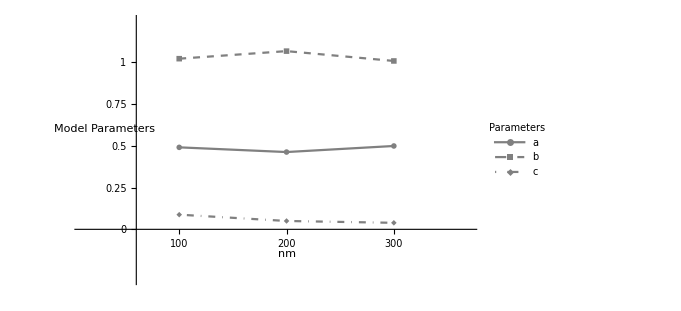

```mathematica
gagAvalueGraph=ListLinePlot[
gagModelParams0, 
PlotRange->{{0.1,3.7},{-0.3,1.25}},AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->Thickness[0.004], BaseStyle->{FontFamily->"Helvetica"},AxesOrigin->{0.6,0},LabelStyle->{FontSize->12,FontWeight->"Bold"},
PlotMarkers->{Automatic,Medium},
PlotLegends-> Placed[LineLegend[{"a","b","c"},LegendMarkers->{Automatic},LegendLabel->Style["Parameters",FontWeight->Bold]],{{0.95,0.6},{0.7,0.5}}],
PlotStyle->{Gray,Directive[Gray,Dashed],Directive[Gray,DotDashed]},Ticks->{{{1,"100"},{2,"200"},{3,"300"}},{0,0.25,0.5,0.75,1}},Epilog->{Text["nm",{2,-0.15},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["Model Parameters",{0.3,0.6},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.C-valueFiberDiam.png",gagAvalueGraph]
```

140917.C-valueFiberDiam.png

```mathematica
Export["140917.C-valueFiberDiam.pdf",gagAvalueGraph]
```

140917.C-valueFiberDiam.pdf

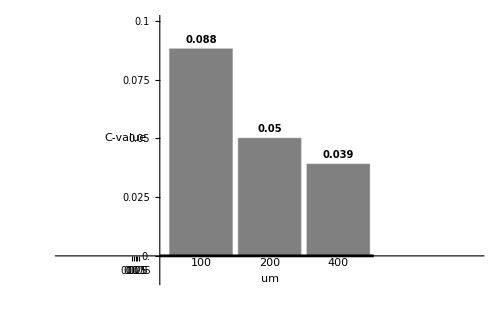

```mathematica
gagCValueGraph=BarChart[gagModelParams1[[3]],
PlotRange->{{-1,5},{-0.01,0.1}},
ChartLabels->{{"100","200","400"}},
AspectRatio->1/GoldenRatio,ImageSize->72*7,AxesStyle->{Directive[Black,Thickness[0.004],FontSize->12],Directive[Black,Thickness[0.004],FontSize->12]}, ChartBaseStyle->{FontFamily->"Helvetica",FontSize->12,FontWeight->Bold},AxesOrigin->{0.4,0},
Ticks->{Table[n,{n,0,0.1,0.025}]},ChartStyle->Gray,TicksStyle->Bold,
LabelingFunction->Above,LabelStyle->{FontWeight->Bold,FontSize->10},
Epilog->{Text["um",{2,-0.01},BaseStyle->{FontSize->12,FontWeight->"Bold"}],Rotate[Text["C-value",{-0.1,0.05},BaseStyle->{FontSize->12,FontWeight->"Bold"}],90 Degree]}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.FiberDiamC-Value.png",gagCValueGraph]
```

140917.FiberDiamC-Value.png

```mathematica
Export["140917.FiberDiamC-Value.pdf",gagCValueGraph]
```

140917.FiberDiamC-Value.pdf

```mathematica
gagModelParams=Prepend[gagModelParams,{"FiberDiamer [um]",100,200,400}];
```

```mathematica
gagModelParams[[4]]
```

{0.088,0.050,0.039}

```mathematica
gagModelParams[[2]]= Prepend[gagModelParams[[2]],"a"];
```

```mathematica
gagModelParams[[3]]= Prepend[gagModelParams[[3]],"b"];
```

```mathematica
gagModelParams[[4]]= Prepend[gagModelParams[[4]],"c"];
```

```mathematica
gagModelParams//InputForm
```

{{"FiberDiamer [um]", 100, 200, 400}, {"a", "0.491", "0.463", "0.499"}, {"b", "1.023", "1.068", "1.009"}, {"c", "0.088", "0.050", "0.039"}}

```mathematica
gagParamsTable=Grid[gagModelParams,Frame->All,ItemSize->{Automatic,2},ItemStyle->{{Bold},{Directive[Bold,FontFamily->"Helvetica"],FontFamily->"Helvetica",FontFamily->"Helvetica",FontFamily->"Helvetica"}},Dividers->{{2->Thick},{2->Thick}}(*,BaseStyle{FontFamily->"Helvetica"}*)]
```

FiberDiamer [um] | 100 | 200 | 400
a | 0.491 | 0.463 | 0.499
b | 1.023 | 1.068 | 1.009
c | 0.088 | 0.050 | 0.039

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Gonzalo\Desktop\Gonzalo\Master thesis\Thermal Imaging\Thermal Imaging Data\140917 Mouse 5(Fiber diameter)

```mathematica
Export["140917.ParamsTableFiberDiam.png",gagParamsTable]
```

140917.ParamsTableFiberDiam.png

```mathematica
Export["140917.ParamsTableFiberDiam.pdf",gagParamsTable]
```

140917.ParamsTableFiberDiam.pdf

```mathematica
{shiftR1,shiftR2, shiftR3}=gagModelShiftFactorRLog[#,stimStart, stimEnd]& /@gagFitDataFiberDiam
```

{-0.256409,-1.35489,-0.228644}

```mathematica
grRPlot=Plot[{funcR1[x+shiftR1*samplingRate],funcR2[x+shiftR1*samplingRate], funcR3[x+shiftR1*samplingRate]},{x,0,(stimEnd+2)*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

```mathematica
{funcF1,funcF2, funcF3}=gagModelFuncFExp[#,fallStart, trialLength]& /@gagFitDataFiberDiam
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.16025×10^-10, 0.00098997, 3.11593×10^-11}, is returned.

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.09209×10^-11, 0.00365925, 2.35278×10^-12}, is returned.

{1.29264 ⅇ^(-0.0136534 (7+#1))+0.589129 ⅇ^(-0.00126295 (90+#1))&,0.959831 ⅇ^(-0.0105641 (7+#1))+0.565246 ⅇ^(-0.00115711 (90+#1))&,0.98866 ⅇ^(-0.0096199 (7+#1))+0.5815 ⅇ^(-0.0010583 (90+#1))&}

```mathematica
grFPlot=Plot[{funcF1[x-(fallStart-stimStart)*samplingRate],funcF2[x-(fallStart-stimStart)*samplingRate], funcF3[x-(fallStart-stimStart)*samplingRate]},{x,(fallStart-stimStart)*samplingRate,trialLength*samplingRate}, PlotStyle->gagColors,PlotRange->All];
```

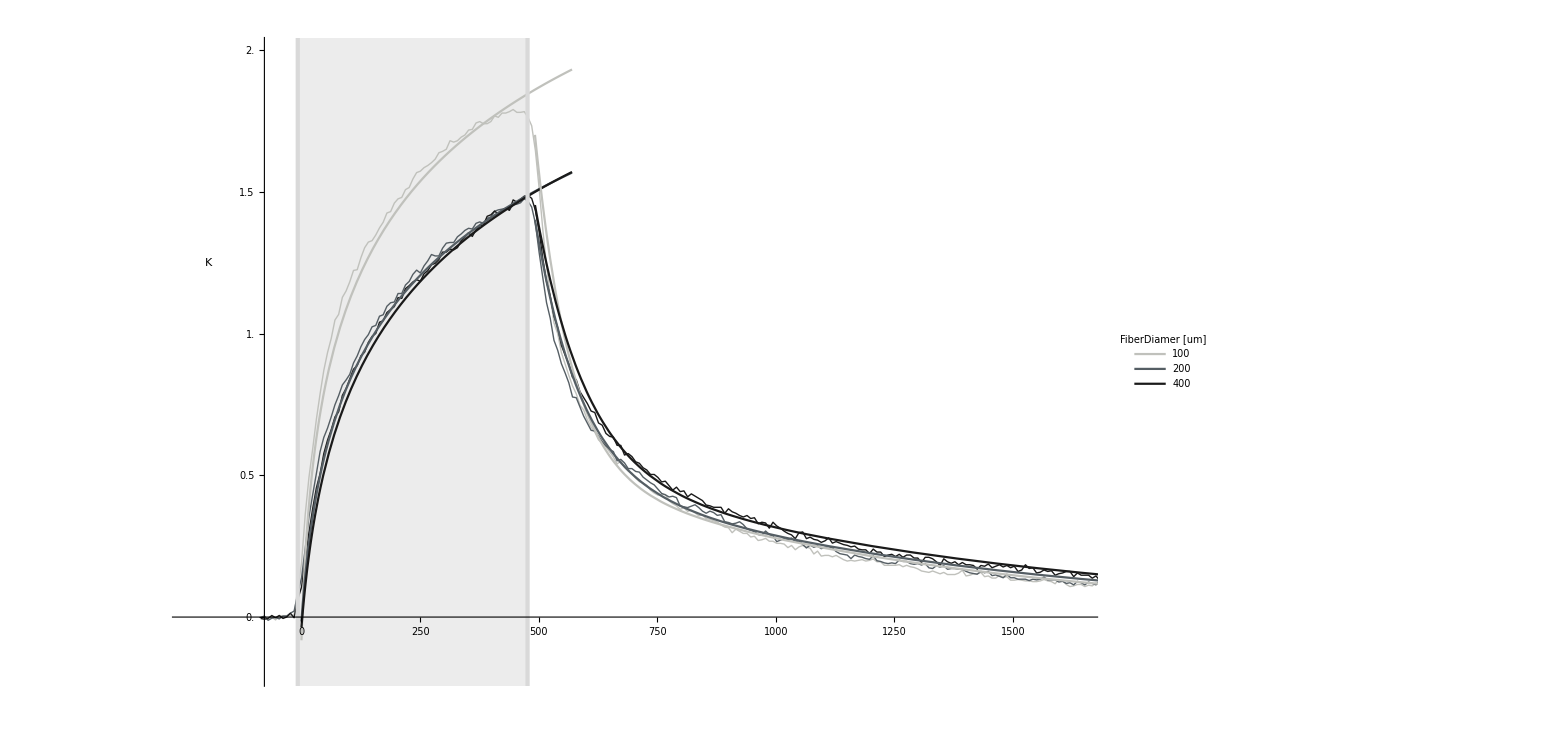

```mathematica
Show[grSDFiberDiam,grRPlot,grFPlot]
```